# Volterra Solvers and Power Spectra -- Particles, multi-species

Created 2025.
Last edited March 2026.
 Email mustafa.a.amin@rice.edu if you have questions or corrections.
 
Please cite the following depending on your usage:
For particle-like DM with Warmth and Poisson :
- single species  Amin, Delos & Mirbabayi (2025)[https://arxiv.org/abs/2503.20881]. Also includes N-body simulations. More general code also available.
- multi-species, Amin, Delos & Yang (2025) [https://arxiv.org/abs/2510.15046]. Also includes (limited) N-body simulations.
For Wave DM with Warmth and Poisson:
- single species,  Amin, May & Mirbabayi (2025) [https://arxiv.org/abs/2506.12131]. Includes nonlinear Schrodinger-Poisson simulations.
- multi-species,   Amin & Delos (2025) [https://arxiv.org/abs/2510.17977]. Most general, can include the particle case also.

## parameters

```mathematica
Quit[];
```

```mathematica
(* ~~~~~~~~Parameters ~~~~~~~~`*)
{y0,y}={10^-3.,10^2.}; (* y-range *)
{kmin,kmax}={0.5, 10^4.}; (* k-range *)
{Ny,Nit,Nk}={800,15,60};(* # of y-divisions, Picard iterations, α samples *)
yout={0.01,0.1,1.,10.,100.}; (* y- values to output power spectra at *)

Mpc=1;
keq=0.01 Mpc^-1;  (* Subscript[k, eq] *)
f2=0.1; (* mass fraction in species 2*)
f1=1-f2; (* mass fraction in species 1*)
{n1,n2}={(f1^2 kwn1^3)/(2 π^2)/.kwn1->10^7. Mpc^-1,(f2^2 kwn2^3)/(2 π^2)/.kwn2->10^3. Mpc^-1}; (* number density of each species *)
{σeq1,σeq2}=(22 (*km s^-1*))/(3 10^5  (*km s^-1*)){10^-4.,1.}; (* velocity dispersion in each species*)
(*{σeq1,σeq2}=22/(3 10^5){1.,10^-4.}; (*Case 2 *)*)
(*{σeq1,σeq2}=22/(3 10^5){10^-4.,10^-4.}; *)(*CDM*)
```

## computation

```mathematica
(*~~~~~ pre-defined functions and grids ~~~~~~*)
(* y-Grid, y-midpoints, and α-grid *)
ygrid=Exp@Subdivide[Log[y0],Log[y],Ny-1]; (* log-spaced y-grid *)
r=(√(ygrid[[2]]/ygrid[[1]])-√(ygrid[[1]]/ygrid[[2]])); (* r = √(Subscript[y, i+1]/Subscript[y, i])-√(Subscript[y, i]/Subscript[y, i+1]) *)
midpts=√(Most[ygrid]*Rest[ygrid]); (* Subscript[m, i]=√(Subscript[y, i+1] Subscript[y, i]) of y-grid,useful for integration, (Subscript[y, i+1]-Subscript[y, i])=Subscript[y, i] r *)
Nmid=Length[midpts]; (* # of y midpoints *)
klist=Exp@Subdivide[Log[kmin],Log[kmax],Nk-1]; (*α-grid*)

(*Precompute k-independent matrices*)
F=Outer[Log[#1/#2 (1+√(1+#2))^2/(1+√(1+#1))^2]&,midpts,midpts]; (* distance function as a matrix of y and y'*)
DY=Outer[(#2 r)/Sqrt[1+#2]&,midpts,midpts]; (* integration measure as a vector *)
mask=LowerTriangularize[ConstantArray[1.,{Nmid,Nmid}],-1]; (* y>y', this is a triangular matrix *)

(*~~~~~ main module ~~~~~~*)
ClearAll[computeT]
computeT[k_,Nit_,F_,DY_,mask_]:=Module[{Tfsa,Tfsb,Tfsc,KK,Ta,Tb,Tc},
(*~~~~~~~~~Free-streaming Kernels for the total spectra~~~~~~~~*)
Tfsa=(f1 Exp[-(k/keq)^2 σeq1^2 F^2]+f2 Exp[-(k/keq)^2 σeq2^2 F^2])*mask;
Tfsb=F*(f1 Exp[-(k/keq)^2 σeq1^2 F^2]+f2 Exp[-(k/keq)^2 σeq2^2 F^2])*mask;
Tfsc=(1/n1 f1^2 Exp[-(k/keq)^2 σeq1^2 F^2]+1/n2 f2^2 Exp[-(k/keq)^2 σeq2^2 F^2])/(1/n1 f1^2+1/n2 f2^2)*mask;
(*~~~~~~~~~Kernel of Volterra Eq. ~~~~~~~~*)
KK=3/2*DY*Tfsb;
(*~~~~~~~~~Initialize with the free streaming kernels~~~~~~~~*)
Tb=Tfsb;
Ta=Tfsa;
Tc=Tfsc;
(*~~~~~~~~ Iterate ~~~~~~~~*)
Do[
Tb=Tfsb+KK.Tb;
Ta=Tfsa+KK.Ta;
Tc=Tfsc+KK.Tc;,{Nit}];
{k,Ta,Tb,Tc}]

(*~~~~~~~ execute to get the transfer functions ~~~~~~~*)
(*Run the computation in parallel*)
{t,results}=AbsoluteTiming[ParallelTable[computeT[k,Nit,F,DY,mask],{k,klist}]]; (* results holds the data, t is time taken *)
Print["Total time for ",Length[klist]," α values: ",t," seconds"];
```

Total time for 60 α values: 14.6568 seconds

```mathematica
(*~~~~~~~ Power Spectrum Data  generation ~~~~~~~*)

(*~~~~~~~ Isocurvature ~~~~~~~*)
dy=(r midpts)/(√(1+midpts)); (* integration measure *)
(* Compute Subscript[P^(iso), δ](y,k)/P^(iso)(Subscript[y, 0],k) for each y*)
(* First T^(a,c) are extracted from results and then the PS evolution is constructed *)
PowerSpectra=Table[Module[{i0,PSY},i0=Nearest[midpts->"Index",Y][[1]];
PSY=Table[With[{Tb=results[[j,3]],Tc=results[[j,4]]},1+3 (dy[[1;;i0-1]].(Tc[[i0,1;;i0-1]]*Tb[[i0,1;;i0-1]]))],{j,Length[results]}];
{midpts[[i0]],PSY}],{Y,yout}];
(*Extract k list*)
kk=results[[All,1]];

plotData=Table[Transpose[{kk,PowerSpectra[[j,2]]}],{j,Length[yout]}];(* This is data in the form of (k, Subscript[P^(iso), δ](y,k)/P^(iso)(Subscript[y, 0],k) for each y*)
```

```mathematica
(*~~~~~~~ Adiabatic ~~~~~~~*)
PR[j_]:=2 10^-9(36(3+Log[0.15 klist[[j]]/keq]-Log[4/y0])^2); (* the initial subhorizon spectrum*)
dlnPdlny[j_]:=2/(3+Log[0.15 klist[[j]]/keq]-Log[4/y0]); (* log y derivative of the initial spectrum *)
(*Compute Subscript[P, δ](k) for each y*)
PowerSpectraA=Table[Module[{i0,PSYA},i0=Nearest[midpts->"Index",Y][[1]];
PSYA=Table[With[{Ta=results[[j,2]],Tb=results[[j,3]]},PR[j](Ta[[i0,1]]+1/2 √(1+y0) dlnPdlny[j] Tb[[i0,1]])^2],{j,Length[results]}];
{midpts[[i0]],PSYA}],{Y,yout}];
(*Extract alpha list*)
kk=results[[All,1]];
plotDataA=Table[Transpose[{kk,PowerSpectraA[[j,2]]}],{j,Length[yout]}];
```

## Plotting the Results

```mathematica
labeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
xlabeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
ylabeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
unlabeledTicks=Flatten[Table[
{k*j,Null},{k,2,9},{j,labeledTicks[[All,1]]}],1];
xmyTicks=Join[xlabeledTicks,unlabeledTicks];
ymyTicks=Join[ylabeledTicks,unlabeledTicks];
NullmyTicks=Join[unlabeledTicks];
nn=Length[yout];
(*Matplotlib-like cool->warm (blue->white->red)*)
coolwarm=(*ColorData["RedBlueTones"]/@Subdivide[0,1,nn-1];*)
Blend[{RGBColor[59/255,76/255,192/255],RGBColor[98/255,130/255,234/255],RGBColor[141/255,176/255,254/255],RGBColor[185/255,210/255,237/255],RGBColor[221/255,221/255,221/255],RGBColor[245/255,196/255,173/255],RGBColor[244/255,152/255,120/255],RGBColor[221/255,96/255,78/255],RGBColor[180/255,4/255,38/255]},#]&;
(*one color per curve*)
coolwarmColors=coolwarm/@Subdivide[0,1,nn-1];
styles=Directive[Thick,#]&/@coolwarmColors;
```

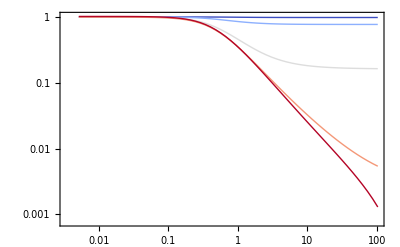

```mathematica
dy=(r midpts)/(√(1+midpts));
(*Compute Subscript[P, δ](alpha_k) for each y*)
PowerSpectra=Table[Module[{i0,PSY},i0=Nearest[midpts->"Index",Y][[1]];
PSY=Table[With[{Ta=results[[j,2]],Tb=results[[j,3]],Tc=results[[j,4]]},1+3 (dy[[1;;i0-1]].(Tc[[i0,1;;i0-1]]*Tb[[i0,1;;i0-1]]))],{j,Length[results]}];
{midpts[[i0]],PSY}],{Y,yout}];
(*Extract alpha list*)
kk=results[[All,1]];

(*Prepare plot data:one series per yout*)
plotData=Table[Transpose[{√2 kk/keq σeq2(*kk*),(*kk^3/(2 π^2)*)(*(f1^2/n1+ f2^2/n2)*)PowerSpectra[[j,2]]/(1PowerSpectraCDM[[j,2]])}],{j,Length[yout]}];

plotIso=ListLogLogPlot[plotData,Joined->True,PlotMarkers->None,PlotStyle->styles,(* <-use the colors here*)(*FrameLabel->{{"((P^(iso))_δ(y,k))/((P^(iso))_δ(y,k)|_cdm)"," "},{"α_(2, k)"(*"k[Mpc^-1]"*)," "}}*)Frame->True,BaseStyle->{Black,FontFamily->"Latin Modern Roman",FontSize->23},ImageSize->400,PlotRange->{All,All},FrameTicks->{{ymyTicks,NullmyTicks},{xmyTicks,NullmyTicks}}]
```

### CDM ISO

```mathematica
dy=(r midpts)/(√(1+midpts));
PowerSpectraCDM=Table[Module[{i0,PSY},i0=Nearest[midpts->"Index",Y][[1]];
PSY=Table[With[{Ta=results[[j,2]],Tb=results[[j,3]],Tc=results[[j,4]]},1+3 (dy[[1;;i0-1]].(Tc[[i0,1;;i0-1]]*Tb[[i0,1;;i0-1]]))],{j,Length[results]}];
{midpts[[i0]],PSY}],{Y,yout}];
```

## Adiabatic Spectrum

```mathematica
labeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
xlabeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
ylabeledTicks=Table[{10^(2i),Superscript[10,2i]},{i,-20,15}];
unlabeledTicks=Flatten[Table[
{k*j,Null},{k,2,9},{j,labeledTicks[[All,1]]}],1];
xmyTicks=Join[xlabeledTicks,unlabeledTicks];
ymyTicks=Join[ylabeledTicks,unlabeledTicks];
NullmyTicks=Join[unlabeledTicks];
FrameTicks->{{xmyTicks,NullmyTicks},{ymyTicks,NullmyTicks}};
```

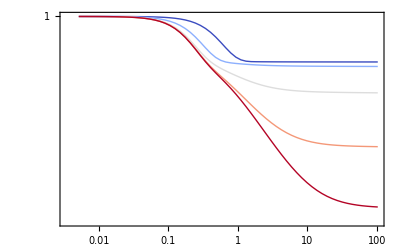

```mathematica
Clear[PR,dlnPdlny]
PR[j_]:=2 10^-9(36(3+Log[0.15 klist[[j]]/keq]-Log[4/y0])^2);
dlnPdlny[j_]:=2/(3+Log[0.15 klist[[j]]/keq]-Log[4/y0]);
(*y0=10^-3.;*)
(*Compute Subscript[P, δ](alpha_k) for each y*)
PowerSpectraA=Table[Module[{i0,PSYA},i0=Nearest[midpts->"Index",Y][[1]];
PSYA=Table[With[{Ta=results[[j,2]],Tb=results[[j,3]]},PR[j](Ta[[i0,1]]+1/2 √(1+y0) dlnPdlny[j] Tb[[i0,1]])^2],{j,Length[results]}];
{midpts[[i0]],PSYA}],{Y,yout}];
(*Extract alpha list*)
kk=results[[All,1]];

(*Prepare plot data:one series per yout*)
plotDataAd=Table[Transpose[{√2 kk/keq σeq2,PowerSpectraA[[j,2]]/PowerSpectraACDM[[j,2]] }],{j,Length[yout]}];
(*Plot*)
(*scaleFactor=α2/α1;*)
plotAd=ListLogLogPlot[plotDataAd,(*PlotLegends->Placed[LineLegend[Table["y = "<>ToString@NumberForm[PowerSpectraA[[j,1]],2],{j,Length[yout]}]],Right],*)Frame->True(*,FrameLabel->{{"((P^(ad))_δ(y,k))/((P^(ad))_δ(y,k)|_cdm)"," "},{"α_(2, k)"," "}},*),Joined->True,PlotStyle->styles,PlotMarkers->None,PlotStyle->{{(*Dashed,*) Opacity[1.]}},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->23},ImageSize->400,PlotRange->{All,All},(*GridLines->Automatic,*)(*FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},*)FrameTicks->{{Automatic,Automatic}(*{ymyTicks,NullmyTicks}*),{xmyTicks,NullmyTicks}}]
```

```mathematica
√□
```

### CDM Ad

```mathematica
dy=(r midpts)/(√(1+midpts));
PowerSpectraCDM=Table[Module[{i0,PSY},i0=Nearest[midpts->"Index",Y][[1]];
PSY=Table[With[{Ta=results[[j,2]],Tb=results[[j,3]],Tc=results[[j,4]]},1+3 (dy[[1;;i0-1]].(Tc[[i0,1;;i0-1]]*Tb[[i0,1;;i0-1]]))],{j,Length[results]}];
{midpts[[i0]],PSY}],{Y,yout}];
```

```mathematica
PR[j_]:=2 10^-9(36(3+Log[0.15 klist[[j]]/keq]-Log[4/y0])^2);
dlnPdlny[j_]:=2/(3+Log[0.15 klist[[j]]/keq]-Log[4/y0]);
PowerSpectraACDM=Table[Module[{i0,PSYA},i0=Nearest[midpts->"Index",Y][[1]];
PSYA=Table[With[{Ta=results[[j,2]],Tb=results[[j,3]]},PR[j](Ta[[i0,1]]+1/2 √(1+y0) dlnPdlny[j] Tb[[i0,1]])^2],{j,Length[results]}];
{midpts[[i0]],PSYA}],{Y,yout}];
```

# Intra/Inter PS

```mathematica
N1=134217728;
N2=120278;
L=1.38372Mpc;
m2=25998.4 Msun;
```

```mathematica
m2/(2 10^4.)
{N1/L^3,N2/L^3}
```

1.29992 Msun

{5.066×10^7,45398.5}

n2

{5.066×10^7,45398.5}

45594.5

```mathematica
Quit[];
```

```mathematica
(* ~~~~~~~~Parameters ~~~~~~~~`*)
{y0,y}={10^-3.,10^2.}; (* y-range *)
{kmin,kmax}={0.5, 10^4.}; (* k-range *)
{Ny,Nit,Nk}={800,15,60};(* # of y-divisions, Picard iterations, α samples *)
yout={0.01,0.1,1.,10.,100.}; 
yout=yyValues;
(* y- values to output power spectra at *)

Mpc=1;
keq=0.01 Mpc^-1;  (* Subscript[k, eq] *)
f2=0.03; (* mass fraction in species 2*)
f1=1-f2; (* mass fraction in species 1*)
{n1,n2}={(f1^2 kwn1^3)/(2 π^2)/.kwn1->10^7. Mpc^-1,45398.5041536546(*(f2^2 kwn2^3)/(2 π^2)/.kwn2->10^3. Mpc^-1*)}
(* number density of each species *)
{σeq1,σeq2}=(22 (*km s^-1*))/(3 10^5  (*km s^-1*)){10^-4.,3*0.987}; 
(* velocity dispersion in each species*)
(*{σeq1,σeq2}=22/(3 10^5){1.,10^-4.}; (*Case 2 *)*)
(*{σeq1,σeq2}=22/(3 10^5){10^-4.,10^-4.}; *)(*CDM*)
```

{4.76666×10^19,45398.5}

```mathematica
22 3*0.987
```

65.142

## computation of inter and intra

```mathematica
(*~~~~~ pre-defined functions and grids ~~~~~~*)
(* y-Grid, y-midpoints, and α-grid *)
ygrid=Exp@Subdivide[Log[y0],Log[y],Ny-1]; (* log-spaced y-grid *)
r=(√(ygrid[[2]]/ygrid[[1]])-√(ygrid[[1]]/ygrid[[2]])); (* r = √(Subscript[y, i+1]/Subscript[y, i])-√(Subscript[y, i]/Subscript[y, i+1]) *)
midpts=√(Most[ygrid]*Rest[ygrid]); (* Subscript[m, i]=√(Subscript[y, i+1] Subscript[y, i]) of y-grid,useful for integration, (Subscript[y, i+1]-Subscript[y, i])=Subscript[y, i] r *)
Nmid=Length[midpts]; (* # of y midpoints *)
klist=Exp@Subdivide[Log[kmin],Log[kmax],Nk-1]; (*α-grid*)

(*Precompute k-independent matrices*)
F=Outer[Log[#1/#2 (1+√(1+#2))^2/(1+√(1+#1))^2]&,midpts,midpts]; (* distance function as a matrix of y and y'*)
DY=Outer[(#2 r)/Sqrt[1+#2]&,midpts,midpts]; (* integration measure as a vector *)
mask=LowerTriangularize[ConstantArray[1.,{Nmid,Nmid}],-1]; (* y>y' *)

(*~~~~~ main module ~~~~~~*)
ClearAll[computeT]
Piso=(1/n1 f1^2+1/n2 f2^2);
computeT[k_,Nit_,F_,DY_,mask_]:=Module[{Tfsa1,Tfsb1,Tfsc1,Tfsa2,Tfsb2,Tfsc2,KK1,KK2,Ta1,Tb1,Tc1,Ta2,Tb2,Tc2},
(*~~~~~~~~~Free-streaming Kernels for the total spectra~~~~~~~~*)
Tfsa1=(Exp[-(k/keq)^2 σeq1^2 F^2])*mask;
Tfsa2=(Exp[-(k/keq)^2 σeq2^2 F^2])*mask;
Tfsb1=F*(Exp[-(k/keq)^2 σeq1^2 F^2])*mask;
Tfsb2=F*(Exp[-(k/keq)^2 σeq2^2 F^2])*mask;
Tfsc1=(f1/n1 Exp[-(k/keq)^2 σeq1^2 F^2])/Piso*mask;
Tfsc2=(f2/n2 Exp[-(k/keq)^2 σeq2^2 F^2])/Piso*mask;
(*~~~~~~~~~Kernel of Volterra Eq. ~~~~~~~~*)
KK1=3/2*DY*Tfsb1;
KK2=3/2*DY*Tfsb2;
(*~~~~~~~~~Initialize with the free streaming kernels~~~~~~~~*)

Ta1=Tfsa1;
Tb1=Tfsb1;
Tc1=Tfsc1;
Ta2=Tfsa2;
Tb2=Tfsb2;
Tc2=Tfsc2;
(*~~~~~~~~ Iterate ~~~~~~~~*)
Do[
Ta1=Tfsa1+KK1.(f1*Ta1+f2*Ta2);
Tb1=Tfsb1+KK1.(f1*Tb1+f2*Tb2);
Tc1=Tfsc1+KK1.(f1*Tc1+f2*Tc2);
Ta2=Tfsa2+KK2.(f1*Ta1+f2*Ta2);
Tb2=Tfsb2+KK2.(f1*Tb1+f2*Tb2);
Tc2=Tfsc2+KK2.(f1*Tc1+f2*Tc2);
,{Nit}];
{k,Ta1,Tb1,Tc1,Ta2,Tb2,Tc2}]

(*~~~~~~~ execute to get the transfer functions ~~~~~~~*)
(*Run the computation in parallel*)
{t,results}=AbsoluteTiming[ParallelTable[computeT[k,Nit,F,DY,mask],{k,klist}]]; (* results holds the data, t is time taken *)
Print["Total time for ",Length[klist]," α values: ",t," seconds"];
```

Total time for 60 α values: 30.7734 seconds

```mathematica
(*~~~~~~~ Power Spectrum Data  generation ~~~~~~~*)

(*~~~~~~~ Isocurvature ~~~~~~~*)
dy=(r midpts)/(√(1+midpts)); (* integration measure *)
(* Compute Subscript[P^(iso), δ](y,k)/P^(iso)(Subscript[y, 0],k) for each y*)
(* First T^(a,c) are extracted from results and then the PS evolution is constructed *)
PowerSpectra11=Table[Module[{i0,PSY11},i0=Nearest[midpts->"Index",Y][[1]];
PSY11=Table[With[{Tb1=results[[j,3]],Tc1=results[[j,4]]},f1^2/n1+3 f1^2 Piso(dy[[1;;i0-1]].(Tc1[[i0,1;;i0-1]]*Tb1[[i0,1;;i0-1]]))],{j,Length[results]}];
{midpts[[i0]],PSY11}],{Y,yout}];
PowerSpectra22=Table[Module[{i0,PSY22},i0=Nearest[midpts->"Index",Y][[1]];
PSY22=Table[With[{Tb2=results[[j,6]],Tc2=results[[j,7]]},f2^2/n2+3 f2^2 Piso(dy[[1;;i0-1]].(Tc2[[i0,1;;i0-1]]*Tb2[[i0,1;;i0-1]]))],{j,Length[results]}];
{midpts[[i0]],PSY22}],{Y,yout}];
PowerSpectra12=Table[Module[{i0,PSY12},i0=Nearest[midpts->"Index",Y][[1]];
PSY12=Table[With[{Tb1=results[[j,3]],Tc1=results[[j,4]],Tb2=results[[j,6]],Tc2=results[[j,7]]},3/2 f1 f2 Piso(dy[[1;;i0-1]].(Tc2[[i0,1;;i0-1]]*Tb1[[i0,1;;i0-1]]+Tc1[[i0,1;;i0-1]]*Tb2[[i0,1;;i0-1]]))],{j,Length[results]}];
{midpts[[i0]],PSY12}],{Y,yout}];
PowerSpectra21=Table[Module[{i0,PSY21},i0=Nearest[midpts->"Index",Y][[1]];
PSY21=Table[With[{Tb1=results[[j,3]],Tc1=results[[j,4]],Tb2=results[[j,6]],Tc2=results[[j,7]]},3/2 f2 f1 Piso(dy[[1;;i0-1]].(Tc1[[i0,1;;i0-1]]*Tb2[[i0,1;;i0-1]]+Tc2[[i0,1;;i0-1]]*Tb1[[i0,1;;i0-1]]))],{j,Length[results]}];
{midpts[[i0]],PSY21}],{Y,yout}];
(*Extract k list*)
kk=results[[All,1]];

plotData11=Table[Transpose[{√2 kk/keq σeq2,PowerSpectra11[[j,2]]/Piso}],{j,Length[yout]}];
plotData22=Table[Transpose[{√2 kk/keq σeq2,PowerSpectra22[[j,2]]/Piso}],{j,Length[yout]}];
plotData12=Table[Transpose[{√2 kk/keq σeq2,PowerSpectra12[[j,2]]/Piso}],{j,Length[yout]}];
plotData21=Table[Transpose[{√2 kk/keq σeq2,PowerSpectra21[[j,2]]/Piso}],{j,Length[yout]}];
plotData1221=Table[Transpose[{√2 kk/keq σeq2,(PowerSpectra12[[j,2]]+PowerSpectra21[[j,2]])/Piso}],{j,Length[yout]}];
plotDataT=Table[Transpose[{√2 kk/keq σeq2,1/Piso(PowerSpectra11[[j,2]]+PowerSpectra22[[j,2]]+PowerSpectra12[[j,2]]+PowerSpectra21[[j,2]])}],{j,Length[yout]}];(* This is data in the form of (k, Subscript[P^(iso), δ](y,k)/P^(iso)(Subscript[y, 0],k) for each y*)
```

```mathematica
labeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
xlabeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
ylabeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
unlabeledTicks=Flatten[Table[
{k*j,Null},{k,2,9},{j,labeledTicks[[All,1]]}],1];
xmyTicks=Join[xlabeledTicks,unlabeledTicks];
ymyTicks=Join[ylabeledTicks,unlabeledTicks];
NullmyTicks=Join[unlabeledTicks];
nn=Length[yout];
(*Matplotlib-like cool->warm (blue->white->red)*)
coolwarm=(*ColorData["RedBlueTones"]/@Subdivide[0,1,nn-1];*)
Blend[{RGBColor[59/255,76/255,192/255],RGBColor[98/255,130/255,234/255],RGBColor[141/255,176/255,254/255],RGBColor[185/255,210/255,237/255],RGBColor[221/255,221/255,221/255],RGBColor[245/255,196/255,173/255],RGBColor[244/255,152/255,120/255],RGBColor[221/255,96/255,78/255],RGBColor[180/255,4/255,38/255]},#]&;
(*one color per curve*)
coolwarmColors=coolwarm/@Subdivide[0,1,nn-1];
styles=Directive[Thick,#]&/@coolwarmColors;
```

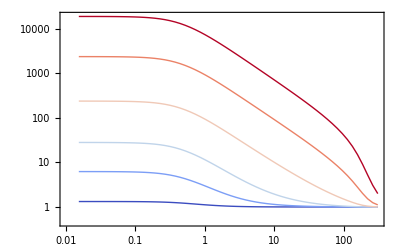

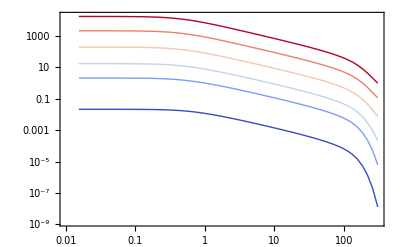

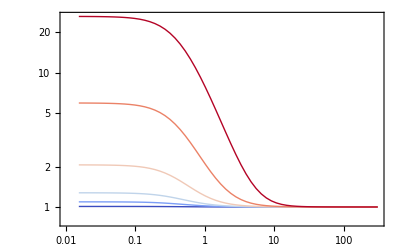

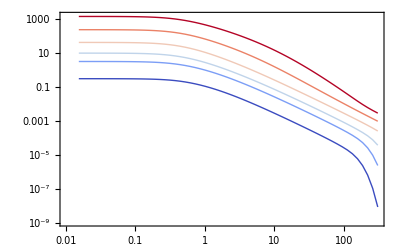

```mathematica
plotIsoT=ListLogLogPlot[plotDataT,Joined->True,PlotMarkers->None,PlotStyle->styles,(* <-use the colors here*)(*FrameLabel->{{"((P^(iso))_δ(y,k))/((P^(iso))_δ(y,k)|_cdm)"," "},{"α_(2, k)"(*"k[Mpc^-1]"*)," "}}*)Frame->True,BaseStyle->{Black,FontFamily->"Latin Modern Roman",FontSize->23},ImageSize->400,PlotRange->{All,All},FrameTicks->{{ymyTicks,NullmyTicks},{xmyTicks,NullmyTicks}}]


plotIso11=ListLogLogPlot[plotData11,Joined->True,PlotMarkers->None,PlotStyle->styles,(* <-use the colors here*)(*FrameLabel->{{"((P^(iso))_δ(y,k))/((P^(iso))_δ(y,k)|_cdm)"," "},{"α_(2, k)"(*"k[Mpc^-1]"*)," "}}*)Frame->True,BaseStyle->{Black,FontFamily->"Latin Modern Roman",FontSize->23},ImageSize->400,PlotRange->{All,All},FrameTicks->{{ymyTicks,NullmyTicks},{xmyTicks,NullmyTicks}}]

plotIso22=ListLogLogPlot[plotData22,Joined->True,PlotMarkers->None,PlotStyle->styles,(* <-use the colors here*)(*FrameLabel->{{"((P^(iso))_δ(y,k))/((P^(iso))_δ(y,k)|_cdm)"," "},{"α_(2, k)"(*"k[Mpc^-1]"*)," "}}*)Frame->True,BaseStyle->{Black,FontFamily->"Latin Modern Roman",FontSize->23},ImageSize->400,PlotRange->{All,All},FrameTicks->{{ymyTicks,NullmyTicks},{xmyTicks,NullmyTicks}}]
plotIso1221=ListLogLogPlot[plotData1221,Joined->True,PlotMarkers->None,PlotStyle->styles,(* <-use the colors here*)(*FrameLabel->{{"((P^(iso))_δ(y,k))/((P^(iso))_δ(y,k)|_cdm)"," "},{"α_(2, k)"(*"k[Mpc^-1]"*)," "}}*)Frame->True,BaseStyle->{Black,FontFamily->"Latin Modern Roman",FontSize->23},ImageSize->400,PlotRange->{All,All},FrameTicks->{{ymyTicks,NullmyTicks},{xmyTicks,NullmyTicks}}]
```

```mathematica
(*~~~~~~~ Adiabatic ~~~~~~~*)
PR[j_]:=2 10^-9(36(3+Log[0.15 klist[[j]]/keq]-Log[4/y0])^2); (* the initial subhorizon spectrum*)
dlnPdlny[j_]:=2/(3+Log[0.15 klist[[j]]/keq]-Log[4/y0]); (* log y derivative of the initial spectrum *)
(*Compute Subscript[P, δ](k) for each y*)
PowerSpectraA=Table[Module[{i0,PSYA},i0=Nearest[midpts->"Index",Y][[1]];
PSYA=Table[With[{Ta=results[[j,2]],Tb=results[[j,3]]},PR[j](Ta[[i0,1]]+1/2 √(1+y0) dlnPdlny[j] Tb[[i0,1]])^2],{j,Length[results]}];
{midpts[[i0]],PSYA}],{Y,yout}];
(*Extract alpha list*)
kk=results[[All,1]];
plotDataA=Table[Transpose[{kk,PowerSpectraA[[j,2]]}],{j,Length[yout]}];
```